Set to current directory (save this notebook first)

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

```mathematica
Import["bone_small.png"]
```

-Graphics-

```mathematica
Import["bone_small.png","Data"] (*See what it is*)
```

{{{87,87,87},{74,74,74},{74,74,74},{74,74,74},{74,74,74},{73,73,73},{95,95,95},{77,77,77},{51,51,51},{44,44,44},{43,43,43},{46,46,46},{55,55,55},20,{74,74,74},{74,74,74},{74,74,74},{74,74,74},{74,74,74},{74,74,74},{74,74,74},{74,74,74},{74,74,74},{74,74,74},{74,74,74},{74,74,74},{87,87,87}},44,{1}}
 |  |  |  |

```mathematica
Map[Map[First,#]&, {{{1,2,3},{4,5,6}},
{{7,8,9},{10,11,12}}}]
```

{{1,4},{7,10}}

```mathematica
Reverse[Map[Map[First,#]&, {{{1,2,3},{4,5,6}},
{{7,8,9},{10,11,12}}}]]
```

{{7,10},{1,4}}

```mathematica
Reverse[Map[Map[First,#]&,Import["bone_small.png","Data"]]]; (*why reverse?*)
```

```mathematica
PNGtoGray[filename_]:=Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
```

```mathematica
img=PNGtoGray["bone_small.png"];
```

```mathematica
showGrayImage[img_]:=Graphics[Raster[img/Max[img]],Frame->False];  (*grey scale image*)
```

```mathematica
showGrayImage[img]
```

-Graphics-

```mathematica
threshold[img_, val_]:=Map[If[#>val,1,0]&,img,{2}]; 
(*pixel value is two levels deep so we have {2} there*)
(* 1 is white, 0 is black *)
```

```mathematica
showBinaryImage[img_]:=Graphics[Raster[img],Frame->False]; (*binary picture*)
```

```mathematica
showBinaryImage[threshold[img,80]]
```

-Graphics-

```mathematica
structSquare={{-1,-1},{-1,0},{-1,1},{0,1},{1,1},{1,0},{1,-1},{0,-1}};
structCross={{0,1},{0,-1},{1,0},{-1,0}};
```

```mathematica
B = threshold[img,80]; (*look at what data it is*)
```

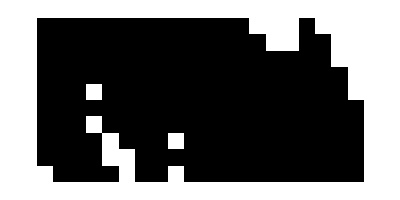

```mathematica
showBinaryImage[B⟦1;;10,1;;20⟧]
```

```mathematica
Length[B]
```

```mathematica
Dimensions[B]
```

{46,46}

```mathematica
(*i=1,j=1;
Select[B⟦i-1;;i+1,j-1;;j+1⟧, *)
```

```mathematica
showBinaryOverlay[img_,mask_]:=Graphics[Raster[MapThread[MapThread[If[#2==1,{1,0,0},{#1,#1,#1}]&,{#1,#2}]&,
{img,mask}]],Frame->False];
```

```mathematica
Do[If[i-1<1 || j-1 <1 ,Print["OOPS"],Print[{i,j}]];,{i,3},{j,3}]
```

OOPS

OOPS

OOPS

«1 more identical outputs»

{2,2}

{2,3}

OOPS

{3,2}

{3,3}

```mathematica
Dimensions[img][[2]]
```

46

```mathematica
Do[Print[i], {i[[1]], structSquare}]
```

Do::write: Tag Part in i⟦1⟧ is Protected.

```mathematica
Do[Print[i⟦1⟧,",",i⟦2⟧],{i,structSquare}]
```

-1,-1

-1,0

-1,1

0,1

1,1

1,0

1,-1

0,-1

```mathematica
erode[img_,str_,r_]:=

Do[
Do[if[i-1<1 || j-1 < 1 || i +1> Dimensions[img]⟦1⟧ || j+1 > Dimensions[img]⟦2⟧,
(*check if out of bounds*), 
img⟦i,j⟧=0;continue[];(*on the edge, paint it black*), 
Do[If[img⟦i+s⟦1⟧,j+⟦2⟧⟧==0,img⟦i,j⟧=2;Break,Continue[]],{s,structSquare}]
(*If any pixel under mask of that location is 0(black), mark it as 2 
;if it is white, then continue *)
]
{i,Dimensions[img]⟦1⟧},{j,Dimensions[img]⟦2⟧}];
,r];
```

```mathematica
Do[
Do[If[Divisible[k,2],Print[k],Print[1]],{k,3}];
Do[If[Divisible[k,2],Print[k],Print[3]],{k,3}];,

3]
```

1

2

1

3

2

3

1

2

1

3

2

3

1

2

1

3

2

3

```mathematica
erode[img_,str_,r_]:= [
Do[
Do[
(*check if out of bounds*) 
if[i-1<1 || j-1 < 1 || i +1> Dimensions[img]⟦1⟧ || j+1 > Dimensions[img]⟦2⟧,
(*if pixel is on the edge, paint it black*)
img⟦i,j⟧=0;continue[];, 
(* Check if the object pixel (0,0) has background pixel (black)
in its square neighborhood -- if it has, then mark it (with 2), o/w continue *)
Do[If[img⟦i+s⟦1⟧,j+⟦2⟧⟧==0,img⟦i,j⟧=2;Break,Continue[]],{s,str}]
],{i,Dimensions[img]⟦1⟧},{j,Dimensions[img]⟦2⟧}];
Do[If[img⟦i,j⟧==2,img⟦i,j⟧==0,Continue[]],{i,Dimensions[img]⟦1⟧},{j,Dimensions[img]⟦2⟧}];
,r]
]
```

Syntax::sntxf: "erode[img_,str_,r_]:=" cannot be followed by "[«1»]".

```mathematica
test[]:= Do[
Do[If[Divisible[k,2],Print[k],Print[1]],{k,3}];
Do[If[Divisible[k,2],Print[k],Print[3]],{k,3}];,

3];
```

```mathematica
erode[img_,str_,r_]:=
Do[
Do[
(*check if out of bounds*) 
if[i-1<1 || j-1 < 1 || i +1> Dimensions[img]⟦1⟧ || j+1 > Dimensions[img]⟦2⟧,
(*if pixel is on the edge, paint it black*)
img⟦i,j⟧=0;, 
(* Check if the object pixel (0,0) has background pixel (black)
in its square neighborhood -- if it has, then mark it (with 2), o/w continue *)
Do[If[img⟦i+s⟦1⟧,j+s⟦2⟧⟧==0,img⟦i,j⟧=2;Break,Continue[]],{s,str}]
],{i,Dimensions[img]⟦1⟧},{j,Dimensions[img]⟦2⟧}];

Do[If[img⟦i,j⟧==2,img⟦i,j⟧==0,Continue[]],
{i,Dimensions[img]⟦1⟧},{j,Dimensions[img]⟦2⟧}];
,r]
```

```mathematica
Dimensions[B]⟦2⟧
```

46

```mathematica
StructSquare={{-1,-1},{-1,0},{-1,1},{0,1},{1,1},{1,0},{1,-1},{0,-1}};
```

```mathematica
Do[Print[i[[1]],i[[2]]],{i,StructSquare}]
```

-1-1

-10

-11

01

11

10

1-1

0-1

```mathematica
false
```

false

```mathematica
true
```

true

```mathematica
a=False;
If[a,Print[1],Print[2]]
```

2

```mathematica
Length[StructSquare]
```

8